```mathematica
Needs["JLink`"];
ReinstallJava[CommandLine->"E:\\Java\\jre7\\bin\\javaw.exe"];
AddToClassPath["C:\\myClass"];
```

```mathematica
Needs["T3OpenInterface`"]
```

Needs::nocont: Context "T3OpenInterface`" was not created when Needs was evaluated.

## Develop Section

## Test Unit

### Test Single

```mathematica
t3OpenObject[my]
```

«JavaObject[com.t3.t3Open]»

```mathematica
Fields[my]
```

String code
String pooledData
String poolingWhat
String symbol

```mathematica
my@code
```

pippo

```mathematica
t3OpenSubscribeLastprice[my,"MI","EQCON","1"]
```

outcome=OK|item=MI.EQCON.1

```mathematica
t3OpenGetSubscribedData[my]
```

{MI.EQCON.1|14.49}

```mathematica
t3OpenObject[GbestBid]
```

«JavaObject[com.t3.t3Open]»

```mathematica
t3OpenSubscribeBestBid1[GbestBid,"MI","EQCON","1"]
```

outcome=KO|item=function=subscribe|item=MI.EQCON.1|schema=best_bid1|errorCode=DUSE

```mathematica
t3OpenGetSubscribedData[GbestBid]
```

{14.58}

```mathematica
t3OpenUnsubscribe[{my,my2,GbestBid}]
```

{Null,Null,Null}

### Test Unit Listable

```mathematica
getT3OpenStatus[]
```

outcome=OK

```mathematica
getT3OpenMarketList[]
```

{{outcome=OK|numElements=21},{element=MI|EQCON},{element=MI|CW},{element=MI|MRT},{element=TLX|ELX},{element=MI|HIMTF},{element=OTC|OBOTC},{element=AK|AKIS},{element=MI|DER},{element=FR|EQXET},{element=EUR|EQPA},{element=LON|EQLSE},{element=MA|EQIBE},{element=EUR|EQAMS},{element=EUR|EQBRU},{element=EUR|EQPSI},{element=FR|EUREX},{element=EUR|LIF},{element=NY|EQNY},{element=NQ|EQNQ},{element=CME|CEQFU},{element=CME|CBOFU}}

```mathematica
getLottiMinimi[]
```

{{Sottostante ,Lotto minimo },{A2A ,5000 },{Acea ,500 },{Ansaldo ,500 },{Atlantia ,500 },{Autogrill ,500 },{Azimut Holding ,500 },{Banca Monte dei Paschi di Siena* ,5000 },{Banca Popolare di Milano ,5000 },{Banco Popolare ,1000 },{Banca Popolare Emilia Romagna ,1000 },{Buzzi Unicem ,100 },{Davide Campari ,1000 },{Diasorin ,500 },{Enel* ,500 },{Enel Green Power ,1000 },{Eni* ,500 },{Erg ,500 },{Exor ,100 },{Fiat* ,500 },{Fiat Industrial ,500 },{Finmeccanica ,500 },{Fondiaria-Sai ,1000 },{Generali* ,100 },{Geox ,500 },{Intesa Sanpaolo* ,1 000 },{Intesa Sanpaolo Risparmio ,1 000 },{Italcementi ,100 },{Lottomatica ,100 },{Luxottica Group ,500 },{Mediaset ,1 000 },{Mediobanca ,500 },{Mediolanum ,500 },{Mondadori ,1 000 },{Parmalat ,1 000 },{Pirelli & C. ,500 },{Prysmian ,100 },{Saipem ,500 },{Salvatore Ferragamo ,500 },{Saras ,1000 },{Snam Rete Gas ,1 000 },{Stmicroelectronics* ,500 },{Telecom Italia* ,1 000 },{Telecom Italia Risparmio ,1 000 },{Tenaris ,500 },{Terna ,5 000 },{Tod's ,100 },{Ubi Banca ,500 },{Unicredit* ,1000 },{Unipol ,500 }}

```mathematica
?getT3OpenTickerSearch
```

getT3OpenTickerSearch[exchange_,market_,type_,pattern_,OptionsPattern[]]
restituisce il risultato di una interrogazione con pattern.
{ipAddress->'127.0.0.1',httpPort→8333}

```mathematica
aa=getT3OpenTickerSearch["MI","EQCON","N","generali"]
```

outcome=OK|numElements=2
element=MI|EQCON|122721|BANCA GENERALI|BGN
element=MI|EQCON|1|GENERALI|G

```mathematica
?formatSearchList
```

formatta il risultato proveniente da getT3OpenTickerSearch

```mathematica
formatSearchList[aa];
```

```mathematica
bb = getT3OpenTickerSearch["MI","DER","N","OPTION*TERNA*09/2013"];
```

```mathematica
formatSearchList[bb];
```

```mathematica
codeList ={{"1",G},{"1",G},{"1",G}}
```

{{1,G},{1,G},{1,G}}

### Richiesta LastPrice, BestBid e BestAsk su un singolo codice

```mathematica
connectedList =t3OpenObject[codeList]
```

{{1,G,«JavaObject[com.t3.t3Open]»},{1,G,«JavaObject[com.t3.t3Open]»},{1,G,«JavaObject[com.t3.t3Open]»}}

```mathematica
{t3OpenSubscribeLastprice[connectedList[[1]][[3]],"MI","EQCON","1"],t3OpenSubscribeBestBid1[connectedList[[2]][[3]],"MI","EQCON","1"],t3OpenSubscribeBestAsk1[connectedList[[3]][[3]],"MI","EQCON","1"]}
```

{outcome=OK|item=MI.EQCON.1,outcome=OK|item=MI.EQCON.1,outcome=OK|item=MI.EQCON.1}

```mathematica
refresh = {t3OpenGetSubscribedData[connectedList[[1]][[3]]],t3OpenGetSubscribedData[connectedList[[2]][[3]]],t3OpenGetSubscribedData[connectedList[[3]][[3]]]}
```

{{MI.EQCON.1|14.39},{MI.EQCON.1|14.38},{MI.EQCON.1|14.4}}

```mathematica
connectedList[[All]][[All,3]]
```

{«JavaObject[com.t3.t3Open]»,«JavaObject[com.t3.t3Open]»,«JavaObject[com.t3.t3Open]»}

```mathematica
t3OpenUnsubscribe[connectedList[[All]][[All,3]]]
```

{Null,Null,Null}

```mathematica
connectedList
```

{{1,G,JLink`Objects`vm1`JavaObject25751778402238465},{1,G,JLink`Objects`vm1`JavaObject32230016154599425},{1,G,JLink`Objects`vm1`JavaObject32947379476889601}}

### Richiesta LastPrice, BestBid e BestAsk su una Lista di codici

```mathematica
codeList01={{721316.,"TRN3I2.30"},{721317.,"TRN3I2.40"},{721318.,"TRN3I2.50"},{721319.,"TRN3I2.60"},{721320.,"TRN3I2.70"},{721321.,"TRN3I2.80"},{721322.,"TRN3I2.90"},{721323.,"TRN3I3"},{721324.,"TRN3I3.10"},{721325.,"TRN3I3.20"},{721326.,"TRN3I3.30"},{721327.,"TRN3I3.40"},{721328.,"TRN3I3.50"},{721329.,"TRN3I3.60"}}
```

{{721316.,TRN3I2.30},{721317.,TRN3I2.40},{721318.,TRN3I2.50},{721319.,TRN3I2.60},{721320.,TRN3I2.70},{721321.,TRN3I2.80},{721322.,TRN3I2.90},{721323.,TRN3I3},{721324.,TRN3I3.10},{721325.,TRN3I3.20},{721326.,TRN3I3.30},{721327.,TRN3I3.40},{721328.,TRN3I3.50},{721329.,TRN3I3.60}}

```mathematica
codeList02=Table[StringDrop[ToString[codeList01[[i,1]]],-1],{i,1,Dimensions[codeList01][[1]]}]
```

{721316,721317,721318,721319,721320,721321,721322,721323,721324,721325,721326,721327,721328,721329}

```mathematica
codeList01[[All,2]]
```

{TRN3I2.30,TRN3I2.40,TRN3I2.50,TRN3I2.60,TRN3I2.70,TRN3I2.80,TRN3I2.90,TRN3I3,TRN3I3.10,TRN3I3.20,TRN3I3.30,TRN3I3.40,TRN3I3.50,TRN3I3.60}

```mathematica
data=Transpose[{codeList02,codeList01[[All,2]]}]
```

{{721316,TRN3I2.30},{721317,TRN3I2.40},{721318,TRN3I2.50},{721319,TRN3I2.60},{721320,TRN3I2.70},{721321,TRN3I2.80},{721322,TRN3I2.90},{721323,TRN3I3},{721324,TRN3I3.10},{721325,TRN3I3.20},{721326,TRN3I3.30},{721327,TRN3I3.40},{721328,TRN3I3.50},{721329,TRN3I3.60}}

```mathematica
connectedList = t3OpenObject[data];
```

```mathematica
Table[t3OpenSubscribeLastprice[connectedList[[i,3]],"MI","DER",connectedList[[i,1]]],{i,1,Dimensions[connectedList][[1]]}];
```

```mathematica
Table[{connectedList[[i,1]],connectedList[[i,2]],t3OpenGetSubscribedData[connectedList[[i,3]]]},{i,1,Dimensions[connectedList][[1]]}]
```

{{721316,TRN3I2.30,{MI.DER.721316|0.0}},{721317,TRN3I2.40,{MI.DER.721317|0.0}},{721318,TRN3I2.50,{MI.DER.721318|0.0}},{721319,TRN3I2.60,{MI.DER.721319|0.0}},{721320,TRN3I2.70,{MI.DER.721320|0.0}},{721321,TRN3I2.80,{MI.DER.721321|0.0}},{721322,TRN3I2.90,{MI.DER.721322|0.0}},{721323,TRN3I3,{MI.DER.721323|0.0}},{721324,TRN3I3.10,{MI.DER.721324|0.0}},{721325,TRN3I3.20,{MI.DER.721325|0.0}},{721326,TRN3I3.30,{MI.DER.721326|0.042}},{721327,TRN3I3.40,{MI.DER.721327|0.0}},{721328,TRN3I3.50,{MI.DER.721328|0.0}},{721329,TRN3I3.60,{MI.DER.721329|0.0}}}

```mathematica
t3OpenUnsubscribe[connectedList[[All,3]]]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
connectedList
```

{{721316,TRN3I2.30,JLink`Objects`vm1`JavaObject19733029169659905},{721317,TRN3I2.40,JLink`Objects`vm1`JavaObject7944849344954369},{721318,TRN3I2.50,JLink`Objects`vm1`JavaObject6361250543960065},{721319,TRN3I2.60,JLink`Objects`vm1`JavaObject16097186848702465},{721320,TRN3I2.70,JLink`Objects`vm1`JavaObject5182676721991681},{721321,TRN3I2.80,JLink`Objects`vm1`JavaObject23645312228786177},{721322,TRN3I2.90,JLink`Objects`vm1`JavaObject9131695089385473},{721323,TRN3I3,JLink`Objects`vm1`JavaObject29752934988251137},{721324,TRN3I3.10,JLink`Objects`vm1`JavaObject13904754186911745},{721325,TRN3I3.20,JLink`Objects`vm1`JavaObject14426263242407937},{721326,TRN3I3.30,JLink`Objects`vm1`JavaObject24431287435526145},{721327,TRN3I3.40,JLink`Objects`vm1`JavaObject32477291967676417},{721328,TRN3I3.50,JLink`Objects`vm1`JavaObject9571517608230913},{721329,TRN3I3.60,JLink`Objects`vm1`JavaObject35946623775277057}}

### Historical Price

```mathematica
?t3OpenGetHDailyClosePrice
```

getHDailyClosePrice[market_String,exchange_String,code_String,fromDate_String,OptionsPattern[]];
get historical daily close price.

```mathematica
getT3OpenStatus[]
```

outcome=OK

```mathematica
Options[t3OpenGetHDailyClosePrice]
```

{Private`ipAddress→127.0.0.1,Private`httpPort→8333,Private`frequency→1D}

```mathematica
data =t3OpenGetHDailyClosePrice["MI","EQCON","1","20130701"]
```

{{1,20130701,13.72},{2,20130702,13.56},{3,20130703,13.53},{4,20130704,13.91},{5,20130705,13.71},{6,20130708,14.15},{7,20130709,14.25},{8,20130710,13.92},{9,20130711,13.94},{10,20130712,13.75},{11,20130715,13.96},{12,20130716,13.9},{13,20130717,14.08},{14,20130718,14.45},{15,20130719,14.43},{16,20130722,14.52},{17,20130723,14.4},{18,20130724,14.57},{19,20130725,14.55},{20,20130726,14.57}}

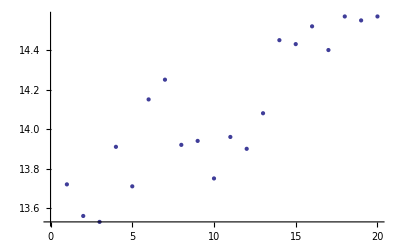

```mathematica
ListPlot[Drop[data,{},{2}]]
```